```mathematica
betaH1ddata5={Log10[#1],Log10[#2]}&@@@Import[NotebookDirectory[]<>"betaH_5ft.csv"];
betaH2ddata5={Log10[#1],Log10[#3]}&@@@Import[NotebookDirectory[]<>"betaH_5ft.csv"];
betaH1ddata10={Log10[#1],Log10[#2]}&@@@Import[NotebookDirectory[]<>"betaH_10ft.csv"];
betaH2ddata10=Drop[{Log10[#1],Log10[#3]}&@@@Import[NotebookDirectory[]<>"betaH_10ft.csv"],{4}];
```

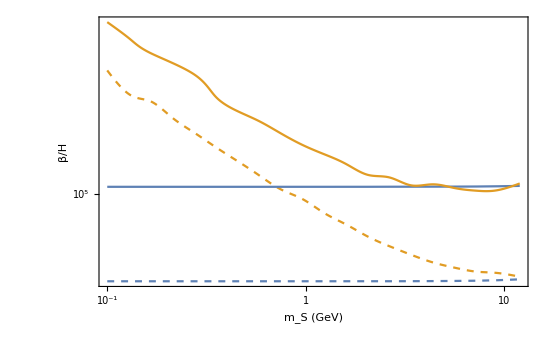

```mathematica
betaH1dplot‵5ft=ListLinePlot[betaH1ddata5,PlotRange->Full,PlotStyle->Dashed];
betaH2dplot‵5ft=ListLinePlot[betaH2ddata5,PlotStyle->Directive[ColorData[97,2],Dashed],InterpolationOrder->3];
betaH1dplot‵10ft=ListLinePlot[betaH1ddata10,PlotRange->Full];
betaH2dplot‵10ft=ListLinePlot[betaH2ddata10,PlotStyle->Directive[ColorData[97,2]],InterpolationOrder->3];
Show[{betaH1dplot‵5ft,betaH2dplot‵5ft,betaH1dplot‵10ft,betaH2dplot‵10ft},PlotRange->Full,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->22],Style["β/H",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->550,FrameTicks->{{LogTicks[3,7,1],True},{LogTicks[-2,2,1],True}},Epilog->{Inset[Framed[Column[{LineLegend[{Directive[ColorData[97,2]],Directive[ColorData[97,2],Dashed],Directive[ColorData[97,1]],Directive[ColorData[97,1],Dashed]},{Style["10% fine-tuning, 2d",FontSize->16],Style["5% fine-tuning, 2d",FontSize->16],Style["10% fine-tuning, 1d",FontSize->16],Style["5% fine-tuning, 1d",FontSize->16]}]}],RoundingRadius->5],Scaled[{0.77,0.72}]]}]
```